# Restavracije z Michelinovimi zvezdicami

## Opis in ideja teme

Sam se dokaj zanimam o restavracijah, torej je bila logična odločitev, da poskusim analizirati nekaj o njih. Logično se je zdelo, da za analizo uporabim “Svetovni standard” - Michelinove zvezdice. Predstavil bom nekaj različnih grafov in dodal zemljevid vseh restavracij.

## Uvoz podatkov iz Kaggla

Najprej sem seveda uvozil podatke, nekateri so bolj uporabni, nekateri pa manj, torej jih malo počistimo.

```mathematica
data = Import["D:\\Documents\\GitHub\\ROM\\michelin_my_maps.csv", "Table", FieldSeparators -> ",", HeaderLines -> 1, CharacterEncoding -> "UTF8"]//Prepend[#,{"Ime", "Naslov", "Lokacija", "MinCena", "MaxCena", "Valuta", "Tip kuhinje", "GeoŠirina", "GeoDolžina", "Telefon", "URL", "Naslov strani", "Nagrada"} ]& //ResourceFunction["DatasetWithHeaders"]
```

Dataset[<>]

## Čiščenje podatkov

Nekaj vrstic je, ki so popolnoma neuporabne, nekatere so pa čudno formatirane - pa jih popravimo.

```mathematica
precisceni = data // 
Query[All,<|"Ime" -> "Ime", "Naslov" -> "Naslov", "Lokacija" -> "Lokacija", "MinCena" ->"MinCena", "MaxCena" -> "MaxCena", "Valuta" -> "Valuta", "Tip kuhinje" ->"Tip kuhinje", "GeoŠirina"->"GeoŠirina", "GeoDolžina"->"GeoDolžina", "Nagrada"->"Nagrada"|>]//
Query[All, <|  #,"MinCena" -> If[#MinCena == "-", 0, #MinCena] |>&]//
Query[Select[#MinCena > 0&],All]//
Query[All, <|  #,"Nagrada" -> If[#Nagrada == "-", 0, #Nagrada] |>&]//
Query[Select[#Nagrada != 0&],All]
```

Dataset[<>]

```mathematica
pr = precisceni // Query[All, <|  #,"MinCena" -> If[#Valuta == "EUR", #MinCena, CurrencyConvert[Quantity[1,#Valuta],"EUR"]] |>&]
```

```mathematica
Failure[…]
```

Sedaj smo malo prečistili vse, edino kar ni uspelo je sprememba vseh valut v EUR.

## Analiza podatkov

Z lepšo tabelo lahko sedaj vizualiziramo podatke. Pogledali bomo: razmerja med številom 1- 2- in 3- michelinskimi restavracijami, količino zvezdic na valuto,  kakšni tipi kuhinje so, na koncu bo pa še vizualizacija vseh lokacij.

## Razmerje med številom 1-, 2-, in 3-Michelinskih restavracij

```mathematica
analiza1 = precisceni //Query[All,<|"Ime" -> "Ime",  "Nagrada"->"Nagrada"|>]// 
Query[Select[#Nagrada != "Bib Gourmand"&],All]//
Query[GroupBy[#Nagrada&]]
```

Dataset[<>]

```mathematica
PieChart[<|"3 Michelinke"->130,"2 Michelinki"->440,"1 Michelinka"->2391|>,ChartStyle->66, ChartLabels->Automatic]
```

-Graphics-

## Zvezdice na valuto(regijo)

```mathematica
analiza2 =precisceni //Query[All,<|"Ime" -> "Ime", "Valuta" -> "Valuta", "Nagrada"->"Nagrada"|>]// 
Query[Select[#Nagrada != "Bib Gourmand"&],All]//
Query[GroupBy["Valuta"]]
```

Dataset[<>]

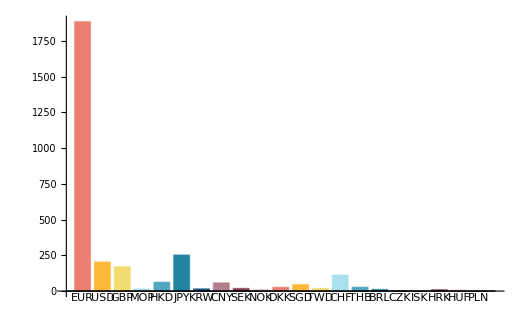

```mathematica
BarChart[<|"EUR"->1886,"USD"->204,"GBP"->171,"MOP"->15,"HKD"->63,"JPY"->253, "KRW"->16, "CNY" ->58, "SEK" ->19, "NOK"->10, "DKK"->27, "SGD"->46,"TWD"->19, "CHF"->113, "THB"->28, "BRL"->12, "CZK"->2, "ISK"->3, "HRK"->10, "HUF"->7, "PLN"->3|>,ChartStyle->24, ChartLabels->Automatic]
```

## Tipi kuhinje

```mathematica
analiza3 =precisceni //Query[All,<|"Ime" -> "Ime", "Tip kuhinje" -> "Tip kuhinje", "Nagrada"->"Nagrada"|>]// 
Query[Select[#Nagrada != "Bib Gourmand"&],All]//
Query[GroupBy["Tip kuhinje"]]
```

Dataset[<>]